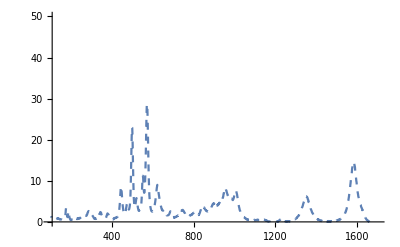

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Raman/RESULTS_Raman/"];
expRaman=ReadList[{"DCmelt011.normalised"}[[1]],{Number,Number,Number}];
Show[{ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1700},{0,50}},PlotStyle->Dashed]}]
```

InterpolatingFunction[{{865.947, 1784.58}}, <>]

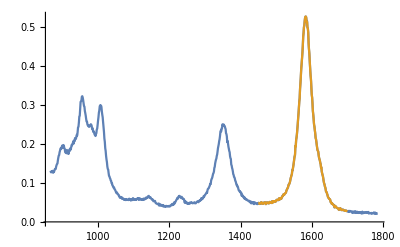

0.075007-0.0000328391 x

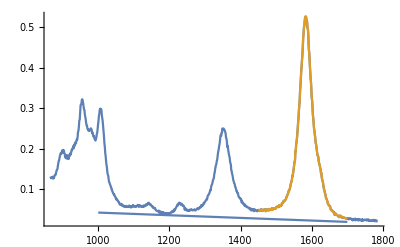

```mathematica
graphite=Transpose[{Transpose[expRaman][[1]],Transpose[expRaman][[3]]}][[210;;1020]];
graphiteInt=Interpolation[graphite]
graphiteTab=Table[{x,graphiteInt[x]},{x,1450,1700}];
graphiteP=ListLinePlot[{graphite,graphiteTab},PlotRange->All]
correction=(graphiteInt[1780]-graphiteInt[1200])/(1780-1200)*x-((graphiteInt[1780]-graphiteInt[1200])/(1780-1260)*x/.x->1200)+graphiteInt[1200]-0.01
Show[{graphiteP,Plot[correction,{x,1000,1700}]},PlotRange->All]
```

```mathematica
model[x_]:=c*PDF[CauchyDistribution[a,b],x]+g*PDF[CauchyDistribution[d,e],x]+correction
model[x]
nonlinFit=NonlinearModelFit[graphiteTab,model[x],{a,b,c,d,e,g},x,MaxIterations->10000]
nonlinFit[[1]][[2]]
```

0.075007-0.0000328391 x+c/(b π (1+(-a+x)^2/b^2))+g/(e π (1+(-d+x)^2/e^2))

FittedModel[0.075007+0.036909/(1+0.00998557 (-«19»+x)^2)+0.50478/(1+0.00253056 («1»)^2)-0.0000328391 x]

{a→1583.08,b→19.8789,c→31.5242,d→1619.34,e→10.0072,g→1.16037}

```mathematica
nonlinFit[[1]][[2]][[1;;3]]
nonlinFit[[1]][[2]][[4;;6]]
nonlinFit[[1]][[-1]][[2]][[1]]
nonlinFit[[1]][[-1]][[2]][[2]]
nonlinFit[[1]][[-1]][[2]][[3]]
nonlinFit[[1]][[-1]][[2]][[4]]
```

{a→1583.08,b→19.8789,c→31.5242}

{d→1619.34,e→10.0072,g→1.16037}

0.075007

-0.0000328391 x

c/(b π (1+(-a+x)^2/b^2))

g/(e π (1+(-d+x)^2/e^2))

```mathematica
nonlinFit[[1]][[2]][[4]]
```

d→1619.34

```mathematica
fit1=nonlinFit[[1]][[-1]][[2]][[3]]/.nonlinFit[[1]][[2]][[1;;3]]
halfmax1=((fit1+2correction)/.x->a/.nonlinFit[[1]][[2]][[1]])/2
fit2=nonlinFit[[1]][[-1]][[2]][[4]]/.nonlinFit[[1]][[2]][[4;;6]]
halfmax2=((fit2+2correction)/.x->d/.nonlinFit[[1]][[2]][[4]])/2
```

0.50478/(1+0.00253056 (-1583.08+x)^2)

0.27541

0.036909/(1+0.00998557 (-1619.34+x)^2)

0.0402838

```mathematica
fit2
halfmax2
```

0.036909/(1+0.00998557 (-1619.34+x)^2)

0.0402838

```mathematica
Solve[fit2==halfmax2,{x}]
```

{{x→1619.34-2.89648 ⅈ},{x→1619.34+2.89648 ⅈ}}

{{x→1564.93},{x→1601.22}}

36.2827

1583.08

0.5278

{{x→1619.34-2.89648 ⅈ},{x→1619.34+2.89648 ⅈ}}

0.+5.79297 ⅈ

1619.34+0. ⅈ

0.0587383+0. ⅈ

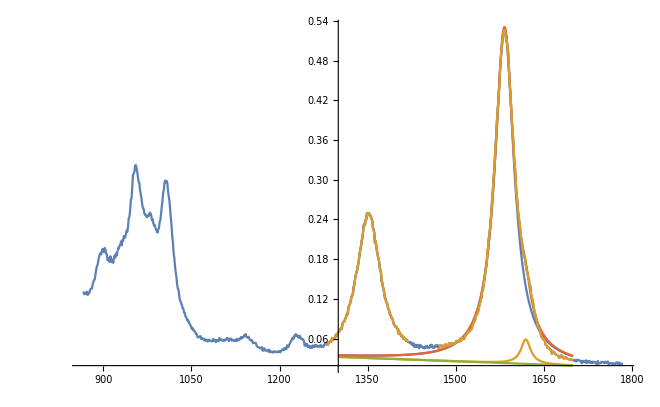

```mathematica
soln1=Solve[fit1==halfmax1,{x}]
FWHM1=soln1[[2]][[1]][[2]]-soln1[[1]][[1]][[2]]
max1=(soln1[[2]][[1]][[2]]+soln1[[1]][[1]][[2]])/2
intens1=(fit1+correction)/.x->max1

soln2=Solve[fit2==halfmax2,{x}]
FWHM2=soln2[[2]][[1]][[2]]-soln2[[1]][[1]][[2]]
max2=(soln2[[2]][[1]][[2]]+soln2[[1]][[1]][[2]])/2
intens2=(fit2+correction)/.x->max2

Show[{Plot[{fit1+correction,fit2+correction,correction,fit1+fit2+correction},{x,1300,1700},PlotRange->All],graphiteP,graphiteP2}]
```

```mathematica
graphiteTabB=Table[{x,graphiteInt[x]},{x,1270,1450}];
modelB[x_]:=j*PDF[CauchyDistribution[h,i],x]+correction
model[x]
nonlinFitB=NonlinearModelFit[graphiteTabB,modelB[x],{h,i,j},x,MaxIterations->10000]
nonlinFitB[[1]][[2]]
```

0.075007-0.0000328391 x+c/(b π (1+(-a+x)^2/b^2))+g/(e π (1+(-d+x)^2/e^2))

FittedModel[0.075007+0.218304/(1+0.00168408 (-«19»+x)^2)-0.0000328391 x]

{h→1351.83,i→24.368,j→16.7121}

```mathematica
nonlinFitB[[1]][[2]][[1;;3]]
```

{h→1351.83,i→24.368,j→16.7121}

```mathematica
nonlinFitB[[1]][[2]][[1;;3]]
nonlinFitB[[1]][[-1]][[2]][[1]]
fit1B=nonlinFitB[[1]][[-1]][[2]][[3]]/.nonlinFitB[[1]][[2]][[1;;3]]
halfmax1B=((fit1B+2*correction)/.x->h/.nonlinFitB[[1]][[2]][[1]])/2
```

{h→1351.83,i→24.368,j→16.7121}

0.075007

0.218304/(1+0.00168408 (-1351.83+x)^2)

0.139766

```mathematica
correction+fit1B
```

0.075007+0.218304/(1+0.00168408 (-1351.83+x)^2)-0.0000328391 x

```mathematica
soln1B=Solve[fit1B==halfmax1B,{x}]
FWHM1B=soln1B[[2]][[1]][[2]]-soln1B[[1]][[1]][[2]]
max1B=(soln1B[[2]][[1]][[2]]+soln1B[[1]][[1]][[2]])/2
intens1B=(fit1B+correction)/.x->max1B
```

{{x→1333.56},{x→1370.1}}

36.5332

1351.83

0.248918

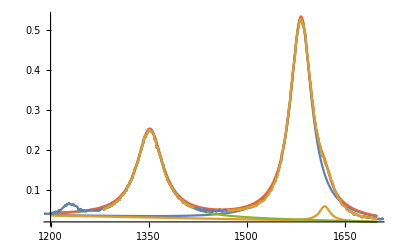

```mathematica
Show[{Plot[{fit1+correction,fit2+correction,fit1B+correction,fit1B+fit1+fit2+correction},{x,1200,1700},PlotRange->{{1200,1700},All}],graphiteP,graphiteP2}]
```

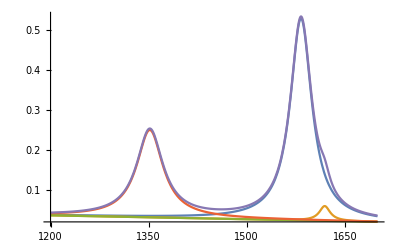

```mathematica
Show[{Plot[{fit1+correction,fit2+correction,correction,fit1B+correction,fit1B+fit1+fit2+correction},{x,1200,1700},PlotRange->All]}]
```

```mathematica
halfmax1B
```

0.124459

```mathematica
graphiteData={{max1B,intens1B},{max1,intens1},{max2,intens2}}
graphiteDataError={{max1B,halfmax1B,FWHM1B/2},{max1,halfmax1,FWHM1/2},{max2,halfmax2,FWHM2/2}}
```

{{1351.83,0.248918},{1583.08,0.5278},{1619.34+0. ⅈ,0.0587383+0. ⅈ}}

{{1351.83,0.139766,18.2666},{1583.08,0.27541,18.1414},{1619.34+0. ⅈ,0.0402838,0.+2.89648 ⅈ}}

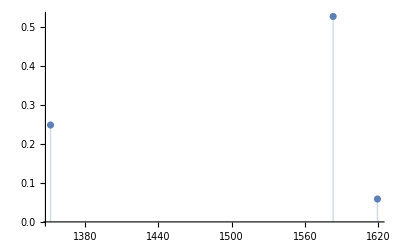

```mathematica
ListPlot[graphiteData,Filling->Bottom]
```

{{{1351.83,0.248918},ErrorBar[{1351.83,0.248918}⟦3⟧,0]},{{1583.08,0.5278},ErrorBar[{1583.08,0.5278}⟦3⟧,0]},{{1619.34+0. ⅈ,0.0587383+0. ⅈ},ErrorBar[{1619.34+0. ⅈ,0.0587383+0. ⅈ}⟦3⟧,0]}}

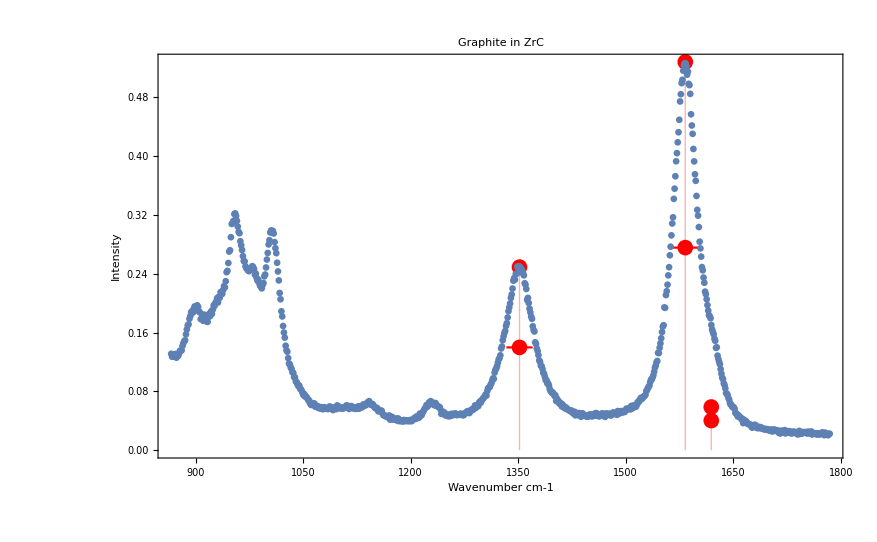

```mathematica
f[x_]:={{x[[1]],x[[2]]},ErrorBar[x[[3]],0]}
f/@graphiteData
Needs["ErrorBarPlots`"]
Show[{ListPlot[graphiteData,Filling->Bottom,Frame->True,PlotStyle->Red],ErrorListPlot[f/@graphiteDataError,PlotStyle->Red] ,ListPlot[graphite]},PlotRange->All,PlotLabel->"Graphite in ZrC",FrameLabel->{"Wavenumber cm-1","Intensity"}]
```

{{{1351.83,0.248918},ErrorBar[{1351.83,0.248918}⟦3⟧,0]},{{1583.08,0.5278},ErrorBar[{1583.08,0.5278}⟦3⟧,0]},{{1619.34,0.0587383},ErrorBar[{1619.34,0.0587383}⟦3⟧,0]}}

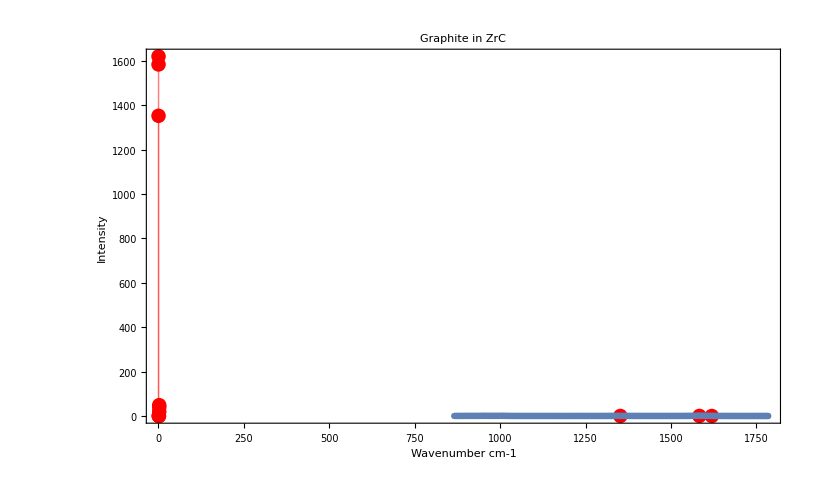

```mathematica
{{{1351.8315165855627,0.24891815146966506},ErrorBar[{1351.8315165855627,0.24891815146966506}⟦3⟧,0]},{{1583.0751007812398,0.5278004888597062},ErrorBar[{1583.0751007812398,0.5278004888597062}⟦3⟧,0]},{{1619.3440233290476,0.05873828671220253},ErrorBar[{1619.3440233290476,0.05873828671220253}⟦3⟧,0]}}
```

```mathematica
Variance@{0.01,0.01,1,5,10}
StandardDeviation@{0.01,0.01,1,5,10}
```

18.668

4.32065

```mathematica
Variance@({0.01,0.01,1,5,10}/2)
StandardDeviation@({0.01,0.01,1,5,10}/2)
```

4.66701

2.16033

```mathematica
list1={0.01,0.01,1,5,10}
list2={0.01,0.01,0.5,5,10}
list3={0.01,0.01,1,5,8}
```

{0.01,0.01,1,5,10}

{0.01,0.01,0.5,5,10}

{0.01,0.01,1,5,8}

```mathematica
var=Variance[Transpose@{list1,list2,list3}]//N
sd=StandardDeviation[Transpose@{list1,list2,list3}]//N
```

{18.668,19.269,12.672}

{4.32065,4.38965,3.55978}

```mathematica
var[[1]]/var[[2]]
var[[1]]/var[[3]]
sd[[1]]/sd[[2]]
sd[[1]]/sd[[3]]
```

0.96881

1.47317

0.984281

1.21374